## Get helper functions

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"UTILITY_readBeamFiles.nb"}]]
```

## Import

```mathematica
tcavSettings={"-90","off","+90"};
L2Settings = {(*"-31.2",*)"-33.2","-35.2","-37.2","-39.2"};
```

```mathematica
allData = Table[
{tcavSetting,L2Setting}->readBeamFile["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/beams/"<>tcavSetting<>"_"<>L2Setting<>"_DTOTR.h5"],
{tcavSetting, tcavSettings},
{L2Setting, L2Settings}
];
allData=Association[Flatten[allData,1]];
```

```mathematica
(*allFiles =Table[
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/beams/"<>tcavSetting<>"_"<>L2Setting<>"_DTOTR.h5",
{tcavSetting, tcavSettings},
{L2Setting, L2Settings}
]//Flatten*)
```

```mathematica
(*allData = readBeamFile[#]&/@allFiles;*)
```

## Visualize

```mathematica
ParallelTable[
Rasterize[densityHistogramMod[10^3{#x,#y}&/@allData[{tcavSetting,L2Setting}],{200,200},LabelStyle->20,ImageSize->400,PlotRange->{{-2,2},{-2.5,0.5}},AspectRatio->Automatic,PlotLabel->{tcavSetting,L2Setting}],RasterSize->800],
{tcavSetting, tcavSettings},
{L2Setting, L2Settings}
]//GraphicsGrid
```

-Graphics-

```mathematica
ParallelTable[
Rasterize[densityHistogramMod[{10^3#z,#pz}&/@allData[{tcavSetting,L2Setting}],{200,200},LabelStyle->20,ImageSize->400,PlotLabel->{tcavSetting,L2Setting}],RasterSize->800],
{tcavSetting, {"off"}},
{L2Setting, L2Settings}
]//GraphicsGrid
```

-Graphics-

## Bin by y-slice

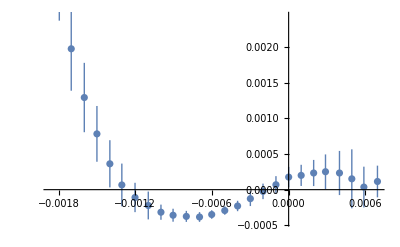

```mathematica
groupedData = GroupBy[allData[[1]],Round[#y,100*^-6]&];

ListPlot[
{Mean[#[[All,"y"]]],Around[#[[All,"x"]]]}&/@Values[groupedData]
]
```

```mathematica
allGroupedData=Table[
 GroupBy[allData[{tcavSetting,L2Setting}],Round[#y,100*^-6]&],
{tcavSetting, tcavSettings},
{L2Setting, {"-37.2"}}
]//Flatten;
```

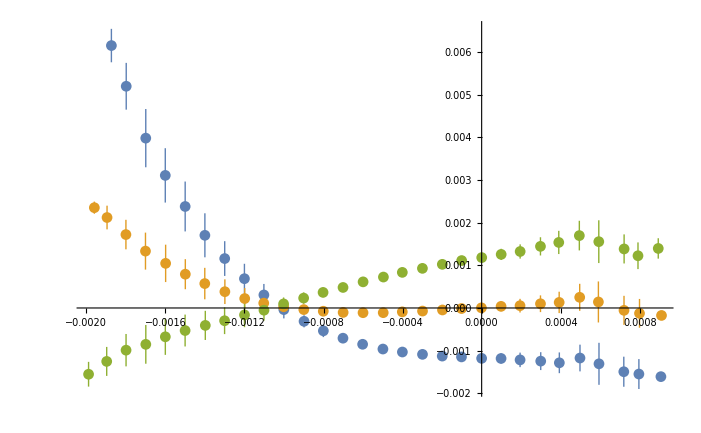

```mathematica
ListPlot[
{Mean[#[[All,"y"]]],Around[#[[All,"x"]]]}&/@Values[#]&/@allGroupedData
]
```

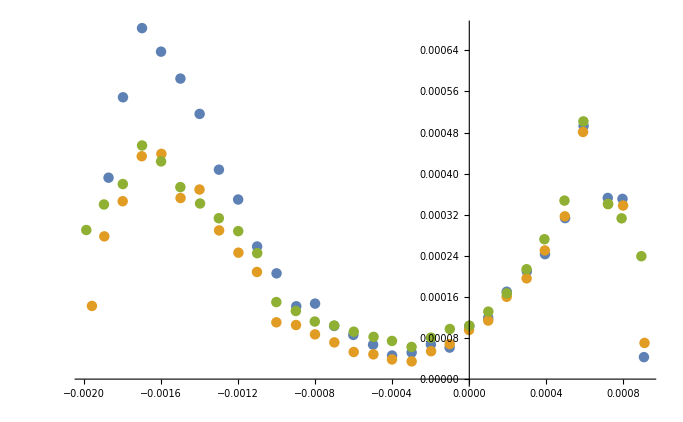

```mathematica
ListPlot[
{Mean[#[[All,"y"]]],StandardDeviation[#[[All,"x"]]]}&/@Values[#]&/@allGroupedData
]
```